# Running in the Rain

## Predicting Runs based on Environmental Data

Stephen Schroeder

## Introduction

I have been running for several years now, and in September of 2017 I decided that I would start a "run streak." A running streak is defined as running at least 1 mile (1.61 km) every calendar day consecutively. I did this mostly because I found that I couldn't stick to only running 3 or 4 days a week - I would suddenly find myself not having run for several weeks or months! 

Now, almost two years later I have ideas about things that might affect my running, but Wolfram Language allows for so much interesting analysis to be done with my data tracked using RunKeeper! Normally I don’t go out with a plan for how long I will run, and I turn back based on how I am feeling that day. Because of this, one of the main questions that I have about my running data is how my running is affected by temperature. I know that I run less in the Canadian winter, but exactly how much less?

## Running Data Preparation

### Importing Running Data

Previously, I used ServiceConnect to fetch my running data, but unfortunately ServiceConnect does not fetch GPS data from RunKeeper which I will need to be able to get environmental data based on the location, date, and time of my run. 
So, I manually exported my data from my RunKeeper account as explained here, and saved the data to my NotebookDirectory[] with all the GPS files in their own folder. Now, to get started, all the data needs to be imported. I imported the data in the same fashion that was done in this fantastic Wolfram Blog post, where the running data is SemanticImported using the column types of the .csv file from RunKeeper.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data = SemanticImport["cardioActivities.csv",{"String","Date","String","String",Restricted["Quantity","Kilometers"],"String","String",Restricted["Quantity",("Kilometers")/("Hours")],Restricted["Quantity","LargeCalories"],Restricted["Quantity","Meters"],"String","String","String","String"}]
```

Dataset[<>]

```mathematica
Import[StringJoin["GPS Data\\",#],"Data"]&/@data[All,"GPX File"]
```

Failure[…]

```mathematica
Import[StringJoin["GPS Data\\",data[[1,"GPX File"]]],"Data"]
```

{{LayerName→Tracks,Geometry→{Line[{GeoPosition[…]}]},Labels→{Name,PointElevation,PointTimestamp,Timestamp},LabeledData→{Name→{Running 6/25/19 7:34 am},PointElevation→{{{35.8 m,35.9 m,35.9 m,35.8 m,35.5 m,35.1 m,34.6 m,34. m,33.3 m,32.5 m,31.5 m,30.5 m,29.5 m,28.4 m,27.3 m,26.3 m,25.4 m,24.5 m,23.6 m,22.9 m,22.3 m,21.6 m,20.9 m,20.3 m,19.6 m,19.1 m,18.6 m,18.2 m,17.8 m,17.5 m,17.1 m,16.7 m,16.5 m,16.5 m,16.5 m,16.5 m,16.7 m,16.9 m,17.2 m,17.5 m,17.8 m,18.2 m,18.5 m,18.9 m,19.2 m,19.5 m,19.6 m,19.7 m,19.8 m,19.9 m,20.1 m,20.3 m,20.5 m,20.7 m,21.1 m,21.5 m,22.1 m,22.6 m,23.3 m,24. m,24.8 m,25.5 m,26.2 m,26.8 m,27.5 m,28.1 m,28.7 m,29.5 m,30.2 m,30.8 m,31.4 m,31.8 m,32.3 m,32.6 m,32.9 m,33. m,32.9 m,32.8 m,32.7 m,32.6 m,32.5 m,32.2 m,31.9 m,31.5 m,31.3 m,31.1 m,31. m,31.1 m,31. m,30.7 m,30.5 m,30.3 m,30.2 m,30.1 m,30. m,29.9 m,29.9 m,29.9 m,29.9 m,29.9 m,30. m,30.1 m,30.4 m,30.8 m,31.5 m,32.4 m,33.4 m,34.4 m,35.5 m,36.6 m,38.1 m,39.7 m,41.4 m,42.8 m,44.1 m,45.2 m,46.1 m,46.9 m,47.7 m,48.5 m,49. m,49.5 m,49.8 m,50.3 m,50.9 m,51.7 m,52.6 m,53.7 m,55. m,56.3 m,57.6 m,59.1 m,60.4 m,61.4 m,62.2 m,62.7 m,63.1 m,63.3 m,63.3 m,63. m,62.5 m,62. m,61.4 m,60.8 m,60.4 m,60.1 m,59.8 m,59.5 m,59.4 m,59.2 m,59.1 m,59.1 m,59.1 m,59.1 m,59.1 m,59.2 m,59.3 m,59.5 m,59.8 m,60.2 m,60.5 m,60.9 m,61.2 m,61.5 m,61.7 m,62. m,62.1 m,62. m,61.8 m,61.5 m,61.2 m,60.7 m,60.3 m,59.8 m,59.4 m,58.9 m,58.5 m,58.1 m,57.9 m,57.7 m,57.6 m,57.5 m,57.5 m,57.5 m,57.5 m,57.5 m,57.6 m,57.8 m,58. m,58.1 m,58.3 m,58.5 m,58.8 m,59.3 m,59.8 m,60.5 m,61.1 m,61.6 m,62. m,62.3 m,62.5 m,62.5 m,62.4 m,62.2 m,61.8 m,61.5 m,60.9 m,60.3 m,59.7 m,59.2 m,58.8 m,58.5 m,58.3 m,58. m,57.8 m,57.6 m,57.5 m,57.4 m,57.3 m,57.3 m,57.4 m,57.4 m,57.5 m,57.6 m,57.9 m,58.3 m,58.7 m,59.3 m,59.8 m,60.4 m,60.8 m,61.2 m,61.5 m,61.8 m,62.1 m,62.2 m,62.1 m,61.8 m,61.5 m,61.1 m,60.7 m,60.4 m,60.1 m,59.8 m,59.5 m,59.3 m,59.1 m,59.1 m,59.1 m,59.1 m,59.1 m,59.2 m,59.4 m,59.5 m,59.8 m,60.1 m,60.5 m,60.9 m,61.4 m,62. m,62.5 m,63. m,63.3 m,63.3 m,63.2 m,62.8 m,62.3 m,61.5 m,60.5 m,59.4 m,58. m,56.6 m,55.3 m,54. m,52.9 m,51.9 m,51.1 m,50.5 m,50.1 m,49.7 m,49.3 m,48.7 m,48.2 m,47.5 m,46.9 m,46.1 m,45.1 m,43.9 m,42.5 m,41.1 m,39.7 m,38.5 m,37.5 m,36.6 m,35.9 m,35.2 m,34.6 m,34.2 m,33.8 m,33.5 m,33. m,32.5 m,32.1 m,31.6 m,31.1 m,30.5 m,29.8 m,29.1 m,28.4 m,27.6 m,27. m,26.4 m,25.7 m,25. m,24.3 m,23.6 m,23. m,22.4 m,21.8 m,21.4 m,21. m,20.7 m,20.5 m,20.5 m,20.5 m,20.4 m,20.3 m,20.3 m,20.3 m,20.2 m,20.1 m,19.9 m,19.7 m,19.4 m,19. m,18.6 m,18.4 m,18.1 m,17.8 m,17.5 m,17.4 m,17.2 m,17.2 m,17.3 m,17.5 m,17.7 m,18.1 m,18.6 m,19.3 m,19.9 m,20.6 m,21.4 m,22.2 m,23.1 m,24. m,24.9 m,25.9 m,26.9 m,27.9 m,29. m,30.1 m,31.1 m,32.1 m,33. m,33.7 m,34.4 m,35. m,35.4 m,35.8 m,36. m,36. m,36. m}}},PointTimestamp→{{{Tue 25 Jun 2019 11:34:44GMT-4.,Tue 25 Jun 2019 11:34:53GMT-4.,Tue 25 Jun 2019 11:34:57GMT-4.,Tue 25 Jun 2019 11:35:00GMT-4.,Tue 25 Jun 2019 11:35:04GMT-4.,Tue 25 Jun 2019 11:35:08GMT-4.,Tue 25 Jun 2019 11:35:13GMT-4.,Tue 25 Jun 2019 11:35:17GMT-4.,Tue 25 Jun 2019 11:35:21GMT-4.,Tue 25 Jun 2019 11:35:25GMT-4.,Tue 25 Jun 2019 11:35:28GMT-4.,Tue 25 Jun 2019 11:35:31GMT-4.,Tue 25 Jun 2019 11:35:34GMT-4.,Tue 25 Jun 2019 11:35:37GMT-4.,Tue 25 Jun 2019 11:35:40GMT-4.,Tue 25 Jun 2019 11:35:43GMT-4.,Tue 25 Jun 2019 11:35:48GMT-4.,Tue 25 Jun 2019 11:35:51GMT-4.,Tue 25 Jun 2019 11:35:54GMT-4.,Tue 25 Jun 2019 11:35:57GMT-4.,Tue 25 Jun 2019 11:36:00GMT-4.,Tue 25 Jun 2019 11:36:03GMT-4.,Tue 25 Jun 2019 11:36:06GMT-4.,Tue 25 Jun 2019 11:36:10GMT-4.,Tue 25 Jun 2019 11:36:14GMT-4.,Tue 25 Jun 2019 11:36:18GMT-4.,Tue 25 Jun 2019 11:36:22GMT-4.,Tue 25 Jun 2019 11:36:26GMT-4.,Tue 25 Jun 2019 11:36:29GMT-4.,Tue 25 Jun 2019 11:36:32GMT-4.,Tue 25 Jun 2019 11:36:35GMT-4.,Tue 25 Jun 2019 11:36:38GMT-4.,Tue 25 Jun 2019 11:36:41GMT-4.,Tue 25 Jun 2019 11:36:44GMT-4.,Tue 25 Jun 2019 11:36:47GMT-4.,Tue 25 Jun 2019 11:36:50GMT-4.,Tue 25 Jun 2019 11:36:53GMT-4.,Tue 25 Jun 2019 11:36:56GMT-4.,Tue 25 Jun 2019 11:36:59GMT-4.,Tue 25 Jun 2019 11:37:03GMT-4.,Tue 25 Jun 2019 11:37:07GMT-4.,Tue 25 Jun 2019 11:37:11GMT-4.,Tue 25 Jun 2019 11:37:15GMT-4.,Tue 25 Jun 2019 11:37:19GMT-4.,Tue 25 Jun 2019 11:37:23GMT-4.,Tue 25 Jun 2019 11:37:27GMT-4.,Tue 25 Jun 2019 11:37:30GMT-4.,Tue 25 Jun 2019 11:37:34GMT-4.,Tue 25 Jun 2019 11:37:38GMT-4.,Tue 25 Jun 2019 11:37:42GMT-4.,Tue 25 Jun 2019 11:37:45GMT-4.,Tue 25 Jun 2019 11:37:48GMT-4.,Tue 25 Jun 2019 11:37:51GMT-4.,Tue 25 Jun 2019 11:37:54GMT-4.,Tue 25 Jun 2019 11:37:58GMT-4.,Tue 25 Jun 2019 11:38:01GMT-4.,Tue 25 Jun 2019 11:38:05GMT-4.,Tue 25 Jun 2019 11:38:08GMT-4.,Tue 25 Jun 2019 11:38:13GMT-4.,Tue 25 Jun 2019 11:38:16GMT-4.,Tue 25 Jun 2019 11:38:19GMT-4.,Tue 25 Jun 2019 11:38:22GMT-4.,Tue 25 Jun 2019 11:38:25GMT-4.,Tue 25 Jun 2019 11:38:29GMT-4.,Tue 25 Jun 2019 11:38:33GMT-4.,Tue 25 Jun 2019 11:38:41GMT-4.,Tue 25 Jun 2019 11:38:45GMT-4.,Tue 25 Jun 2019 11:38:49GMT-4.,Tue 25 Jun 2019 11:38:54GMT-4.,Tue 25 Jun 2019 11:38:58GMT-4.,Tue 25 Jun 2019 11:39:02GMT-4.,Tue 25 Jun 2019 11:39:05GMT-4.,Tue 25 Jun 2019 11:39:08GMT-4.,Tue 25 Jun 2019 11:39:11GMT-4.,Tue 25 Jun 2019 11:39:15GMT-4.,Tue 25 Jun 2019 11:39:29GMT-4.,Tue 25 Jun 2019 11:39:33GMT-4.,Tue 25 Jun 2019 11:39:37GMT-4.,Tue 25 Jun 2019 11:39:41GMT-4.,Tue 25 Jun 2019 11:39:45GMT-4.,Tue 25 Jun 2019 11:39:49GMT-4.,Tue 25 Jun 2019 11:39:53GMT-4.,Tue 25 Jun 2019 11:40:04GMT-4.,Tue 25 Jun 2019 11:40:09GMT-4.,Tue 25 Jun 2019 11:40:16GMT-4.,Tue 25 Jun 2019 11:40:21GMT-4.,Tue 25 Jun 2019 11:40:25GMT-4.,Tue 25 Jun 2019 11:40:29GMT-4.,Tue 25 Jun 2019 11:40:32GMT-4.,Tue 25 Jun 2019 11:40:37GMT-4.,Tue 25 Jun 2019 11:40:44GMT-4.,Tue 25 Jun 2019 11:40:52GMT-4.,Tue 25 Jun 2019 11:40:58GMT-4.,Tue 25 Jun 2019 11:41:02GMT-4.,Tue 25 Jun 2019 11:41:06GMT-4.,Tue 25 Jun 2019 11:41:09GMT-4.,Tue 25 Jun 2019 11:41:12GMT-4.,Tue 25 Jun 2019 11:41:27GMT-4.,Tue 25 Jun 2019 11:41:32GMT-4.,Tue 25 Jun 2019 11:41:36GMT-4.,Tue 25 Jun 2019 11:41:40GMT-4.,Tue 25 Jun 2019 11:41:44GMT-4.,Tue 25 Jun 2019 11:41:48GMT-4.,Tue 25 Jun 2019 11:41:51GMT-4.,Tue 25 Jun 2019 11:41:55GMT-4.,Tue 25 Jun 2019 11:41:59GMT-4.,Tue 25 Jun 2019 11:42:02GMT-4.,Tue 25 Jun 2019 11:42:09GMT-4.,Tue 25 Jun 2019 11:42:17GMT-4.,Tue 25 Jun 2019 11:42:23GMT-4.,Tue 25 Jun 2019 11:42:32GMT-4.,Tue 25 Jun 2019 11:42:38GMT-4.,Tue 25 Jun 2019 11:42:45GMT-4.,Tue 25 Jun 2019 11:42:50GMT-4.,Tue 25 Jun 2019 11:42:55GMT-4.,Tue 25 Jun 2019 11:43:00GMT-4.,Tue 25 Jun 2019 11:43:05GMT-4.,Tue 25 Jun 2019 11:43:10GMT-4.,Tue 25 Jun 2019 11:43:15GMT-4.,Tue 25 Jun 2019 11:43:19GMT-4.,Tue 25 Jun 2019 11:43:23GMT-4.,Tue 25 Jun 2019 11:43:26GMT-4.,Tue 25 Jun 2019 11:43:31GMT-4.,Tue 25 Jun 2019 11:43:36GMT-4.,Tue 25 Jun 2019 11:43:42GMT-4.,Tue 25 Jun 2019 11:43:46GMT-4.,Tue 25 Jun 2019 11:43:49GMT-4.,Tue 25 Jun 2019 11:43:53GMT-4.,Tue 25 Jun 2019 11:43:57GMT-4.,Tue 25 Jun 2019 11:44:01GMT-4.,Tue 25 Jun 2019 11:44:05GMT-4.,Tue 25 Jun 2019 11:44:09GMT-4.,Tue 25 Jun 2019 11:44:13GMT-4.,Tue 25 Jun 2019 11:44:18GMT-4.,Tue 25 Jun 2019 11:44:23GMT-4.,Tue 25 Jun 2019 11:44:27GMT-4.,Tue 25 Jun 2019 11:44:32GMT-4.,Tue 25 Jun 2019 11:44:36GMT-4.,Tue 25 Jun 2019 11:44:40GMT-4.,Tue 25 Jun 2019 11:44:44GMT-4.,Tue 25 Jun 2019 11:44:48GMT-4.,Tue 25 Jun 2019 11:44:52GMT-4.,Tue 25 Jun 2019 11:44:55GMT-4.,Tue 25 Jun 2019 11:44:59GMT-4.,Tue 25 Jun 2019 11:45:03GMT-4.,Tue 25 Jun 2019 11:45:08GMT-4.,Tue 25 Jun 2019 11:45:13GMT-4.,Tue 25 Jun 2019 11:45:17GMT-4.,Tue 25 Jun 2019 11:45:22GMT-4.,Tue 25 Jun 2019 11:45:26GMT-4.,Tue 25 Jun 2019 11:45:29GMT-4.,Tue 25 Jun 2019 11:45:35GMT-4.,Tue 25 Jun 2019 11:45:40GMT-4.,Tue 25 Jun 2019 11:45:44GMT-4.,Tue 25 Jun 2019 11:45:49GMT-4.,Tue 25 Jun 2019 11:45:53GMT-4.,Tue 25 Jun 2019 11:45:57GMT-4.,Tue 25 Jun 2019 11:46:00GMT-4.,Tue 25 Jun 2019 11:46:03GMT-4.,Tue 25 Jun 2019 11:46:06GMT-4.,Tue 25 Jun 2019 11:46:10GMT-4.,Tue 25 Jun 2019 11:46:14GMT-4.,Tue 25 Jun 2019 11:46:19GMT-4.,Tue 25 Jun 2019 11:46:24GMT-4.,Tue 25 Jun 2019 11:46:28GMT-4.,Tue 25 Jun 2019 11:46:32GMT-4.,Tue 25 Jun 2019 11:46:37GMT-4.,Tue 25 Jun 2019 11:46:40GMT-4.,Tue 25 Jun 2019 11:46:44GMT-4.,Tue 25 Jun 2019 11:46:47GMT-4.,Tue 25 Jun 2019 11:46:51GMT-4.,Tue 25 Jun 2019 11:46:55GMT-4.,Tue 25 Jun 2019 11:46:58GMT-4.,Tue 25 Jun 2019 11:47:02GMT-4.,Tue 25 Jun 2019 11:47:06GMT-4.,Tue 25 Jun 2019 11:47:10GMT-4.,Tue 25 Jun 2019 11:47:14GMT-4.,Tue 25 Jun 2019 11:47:18GMT-4.,Tue 25 Jun 2019 11:47:25GMT-4.,Tue 25 Jun 2019 11:47:31GMT-4.,Tue 25 Jun 2019 11:47:36GMT-4.,Tue 25 Jun 2019 11:47:40GMT-4.,Tue 25 Jun 2019 11:47:46GMT-4.,Tue 25 Jun 2019 11:47:50GMT-4.,Tue 25 Jun 2019 11:47:54GMT-4.,Tue 25 Jun 2019 11:47:57GMT-4.,Tue 25 Jun 2019 11:48:01GMT-4.,Tue 25 Jun 2019 11:48:04GMT-4.,Tue 25 Jun 2019 11:48:07GMT-4.,Tue 25 Jun 2019 11:48:11GMT-4.,Tue 25 Jun 2019 11:48:14GMT-4.,Tue 25 Jun 2019 11:48:18GMT-4.,Tue 25 Jun 2019 11:48:21GMT-4.,Tue 25 Jun 2019 11:48:25GMT-4.,Tue 25 Jun 2019 11:48:29GMT-4.,Tue 25 Jun 2019 11:48:33GMT-4.,Tue 25 Jun 2019 11:48:36GMT-4.,Tue 25 Jun 2019 11:48:39GMT-4.,Tue 25 Jun 2019 11:48:42GMT-4.,Tue 25 Jun 2019 11:48:47GMT-4.,Tue 25 Jun 2019 11:48:51GMT-4.,Tue 25 Jun 2019 11:48:55GMT-4.,Tue 25 Jun 2019 11:49:08GMT-4.,Tue 25 Jun 2019 11:49:13GMT-4.,Tue 25 Jun 2019 11:49:17GMT-4.,Tue 25 Jun 2019 11:49:20GMT-4.,Tue 25 Jun 2019 11:49:24GMT-4.,Tue 25 Jun 2019 11:49:28GMT-4.,Tue 25 Jun 2019 11:49:31GMT-4.,Tue 25 Jun 2019 11:49:34GMT-4.,Tue 25 Jun 2019 11:49:37GMT-4.,Tue 25 Jun 2019 11:49:40GMT-4.,Tue 25 Jun 2019 11:49:44GMT-4.,Tue 25 Jun 2019 11:49:48GMT-4.,Tue 25 Jun 2019 11:49:51GMT-4.,Tue 25 Jun 2019 11:49:54GMT-4.,Tue 25 Jun 2019 11:49:57GMT-4.,Tue 25 Jun 2019 11:50:00GMT-4.,Tue 25 Jun 2019 11:50:03GMT-4.,Tue 25 Jun 2019 11:50:07GMT-4.,Tue 25 Jun 2019 11:50:11GMT-4.,Tue 25 Jun 2019 11:50:14GMT-4.,Tue 25 Jun 2019 11:50:17GMT-4.,Tue 25 Jun 2019 11:50:22GMT-4.,Tue 25 Jun 2019 11:50:30GMT-4.,Tue 25 Jun 2019 11:50:36GMT-4.,Tue 25 Jun 2019 11:50:43GMT-4.,Tue 25 Jun 2019 11:50:47GMT-4.,Tue 25 Jun 2019 11:50:51GMT-4.,Tue 25 Jun 2019 11:50:55GMT-4.,Tue 25 Jun 2019 11:50:58GMT-4.,Tue 25 Jun 2019 11:51:02GMT-4.,Tue 25 Jun 2019 11:51:06GMT-4.,Tue 25 Jun 2019 11:51:10GMT-4.,Tue 25 Jun 2019 11:51:14GMT-4.,Tue 25 Jun 2019 11:51:18GMT-4.,Tue 25 Jun 2019 11:51:22GMT-4.,Tue 25 Jun 2019 11:51:26GMT-4.,Tue 25 Jun 2019 11:51:29GMT-4.,Tue 25 Jun 2019 11:51:32GMT-4.,Tue 25 Jun 2019 11:51:35GMT-4.,Tue 25 Jun 2019 11:51:38GMT-4.,Tue 25 Jun 2019 11:51:42GMT-4.,Tue 25 Jun 2019 11:51:45GMT-4.,Tue 25 Jun 2019 11:51:49GMT-4.,Tue 25 Jun 2019 11:51:52GMT-4.,Tue 25 Jun 2019 11:51:56GMT-4.,Tue 25 Jun 2019 11:52:00GMT-4.,Tue 25 Jun 2019 11:52:05GMT-4.,Tue 25 Jun 2019 11:52:08GMT-4.,Tue 25 Jun 2019 11:52:12GMT-4.,Tue 25 Jun 2019 11:52:15GMT-4.,Tue 25 Jun 2019 11:52:19GMT-4.,Tue 25 Jun 2019 11:52:23GMT-4.,Tue 25 Jun 2019 11:52:29GMT-4.,Tue 25 Jun 2019 11:52:34GMT-4.,Tue 25 Jun 2019 11:52:38GMT-4.,Tue 25 Jun 2019 11:52:43GMT-4.,Tue 25 Jun 2019 11:52:48GMT-4.,Tue 25 Jun 2019 11:52:52GMT-4.,Tue 25 Jun 2019 11:52:57GMT-4.,Tue 25 Jun 2019 11:53:02GMT-4.,Tue 25 Jun 2019 11:53:07GMT-4.,Tue 25 Jun 2019 11:53:11GMT-4.,Tue 25 Jun 2019 11:53:15GMT-4.,Tue 25 Jun 2019 11:53:18GMT-4.,Tue 25 Jun 2019 11:53:21GMT-4.,Tue 25 Jun 2019 11:53:24GMT-4.,Tue 25 Jun 2019 11:53:28GMT-4.,Tue 25 Jun 2019 11:53:31GMT-4.,Tue 25 Jun 2019 11:53:36GMT-4.,Tue 25 Jun 2019 11:53:41GMT-4.,Tue 25 Jun 2019 11:53:46GMT-4.,Tue 25 Jun 2019 11:53:51GMT-4.,Tue 25 Jun 2019 11:53:55GMT-4.,Tue 25 Jun 2019 11:53:59GMT-4.,Tue 25 Jun 2019 11:54:02GMT-4.,Tue 25 Jun 2019 11:54:04GMT-4.,Tue 25 Jun 2019 11:54:06GMT-4.,Tue 25 Jun 2019 11:54:09GMT-4.,Tue 25 Jun 2019 11:54:12GMT-4.,Tue 25 Jun 2019 11:54:16GMT-4.,Tue 25 Jun 2019 11:54:20GMT-4.,Tue 25 Jun 2019 11:54:23GMT-4.,Tue 25 Jun 2019 11:54:27GMT-4.,Tue 25 Jun 2019 11:54:31GMT-4.,Tue 25 Jun 2019 11:54:36GMT-4.,Tue 25 Jun 2019 11:54:42GMT-4.,Tue 25 Jun 2019 11:54:48GMT-4.,Tue 25 Jun 2019 11:54:53GMT-4.,Tue 25 Jun 2019 11:55:00GMT-4.,Tue 25 Jun 2019 11:55:06GMT-4.,Tue 25 Jun 2019 11:55:13GMT-4.,Tue 25 Jun 2019 11:55:19GMT-4.,Tue 25 Jun 2019 11:55:25GMT-4.,Tue 25 Jun 2019 11:55:29GMT-4.,Tue 25 Jun 2019 11:55:35GMT-4.,Tue 25 Jun 2019 11:55:46GMT-4.,Tue 25 Jun 2019 11:55:56GMT-4.,Tue 25 Jun 2019 11:56:00GMT-4.,Tue 25 Jun 2019 11:56:03GMT-4.,Tue 25 Jun 2019 11:56:07GMT-4.,Tue 25 Jun 2019 11:56:11GMT-4.,Tue 25 Jun 2019 11:56:15GMT-4.,Tue 25 Jun 2019 11:56:21GMT-4.,Tue 25 Jun 2019 11:56:24GMT-4.,Tue 25 Jun 2019 11:56:27GMT-4.,Tue 25 Jun 2019 11:56:30GMT-4.,Tue 25 Jun 2019 11:56:33GMT-4.,Tue 25 Jun 2019 11:56:36GMT-4.,Tue 25 Jun 2019 11:56:40GMT-4.,Tue 25 Jun 2019 11:56:43GMT-4.,Tue 25 Jun 2019 11:56:46GMT-4.,Tue 25 Jun 2019 11:56:51GMT-4.,Tue 25 Jun 2019 11:56:55GMT-4.,Tue 25 Jun 2019 11:56:58GMT-4.,Tue 25 Jun 2019 11:57:03GMT-4.,Tue 25 Jun 2019 11:57:07GMT-4.,Tue 25 Jun 2019 11:57:11GMT-4.,Tue 25 Jun 2019 11:57:14GMT-4.,Tue 25 Jun 2019 11:57:17GMT-4.,Tue 25 Jun 2019 11:57:20GMT-4.,Tue 25 Jun 2019 11:57:23GMT-4.,Tue 25 Jun 2019 11:57:27GMT-4.,Tue 25 Jun 2019 11:57:32GMT-4.,Tue 25 Jun 2019 11:57:36GMT-4.,Tue 25 Jun 2019 11:57:39GMT-4.,Tue 25 Jun 2019 11:57:42GMT-4.,Tue 25 Jun 2019 11:57:45GMT-4.,Tue 25 Jun 2019 11:57:48GMT-4.,Tue 25 Jun 2019 11:57:51GMT-4.,Tue 25 Jun 2019 11:57:53GMT-4.,Tue 25 Jun 2019 11:57:55GMT-4.,Tue 25 Jun 2019 11:57:58GMT-4.,Tue 25 Jun 2019 11:58:00GMT-4.,Tue 25 Jun 2019 11:58:02GMT-4.,Tue 25 Jun 2019 11:58:04GMT-4.,Tue 25 Jun 2019 11:58:06GMT-4.,Tue 25 Jun 2019 11:58:08GMT-4.,Tue 25 Jun 2019 11:58:10GMT-4.,Tue 25 Jun 2019 11:58:12GMT-4.,Tue 25 Jun 2019 11:58:14GMT-4.,Tue 25 Jun 2019 11:58:16GMT-4.,Tue 25 Jun 2019 11:58:18GMT-4.,Tue 25 Jun 2019 11:58:21GMT-4.,Tue 25 Jun 2019 11:58:24GMT-4.,Tue 25 Jun 2019 11:58:28GMT-4.,Tue 25 Jun 2019 11:58:33GMT-4.,Tue 25 Jun 2019 11:58:38GMT-4.,Tue 25 Jun 2019 11:58:42GMT-4.,Tue 25 Jun 2019 11:58:46GMT-4.,Tue 25 Jun 2019 11:58:51GMT-4.,Tue 25 Jun 2019 11:58:56GMT-4.,Tue 25 Jun 2019 11:59:00GMT-4.,Tue 25 Jun 2019 11:59:04GMT-4.,Tue 25 Jun 2019 11:59:08GMT-4.,Tue 25 Jun 2019 11:59:12GMT-4.,Tue 25 Jun 2019 11:59:16GMT-4.,Tue 25 Jun 2019 11:59:20GMT-4.,Tue 25 Jun 2019 11:59:24GMT-4.,Tue 25 Jun 2019 11:59:28GMT-4.,Tue 25 Jun 2019 11:59:32GMT-4.,Tue 25 Jun 2019 11:59:37GMT-4.,Tue 25 Jun 2019 11:59:41GMT-4.,Tue 25 Jun 2019 11:59:44GMT-4.,Tue 25 Jun 2019 11:59:47GMT-4.,Tue 25 Jun 2019 11:59:50GMT-4.,Tue 25 Jun 2019 11:59:53GMT-4.,Tue 25 Jun 2019 11:59:56GMT-4.,Tue 25 Jun 2019 12:00:00GMT-4.,Tue 25 Jun 2019 12:00:05GMT-4.,Tue 25 Jun 2019 12:00:08GMT-4.}}},Timestamp→{Tue 25 Jun 2019 11:34:44GMT-4.}}}}

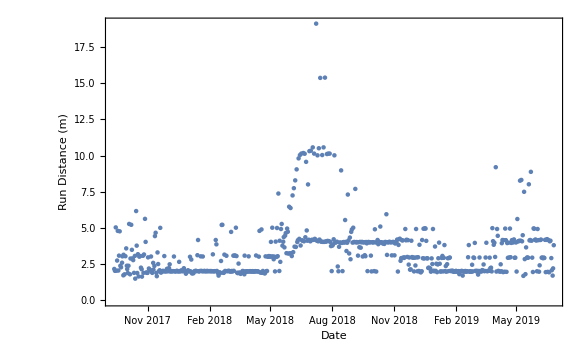

```mathematica
DateListPlot[Query[All,{"Date","Distance (km)"}]@data,Axes->True,FrameLabel->{"Date","Run Distance (m)"},Joined->False,PlotRange->All]
```

```mathematica
WeatherData["Properties"]
```

{AlternateStandardNames,CloudCoverFraction,CloudHeight,CloudTypes,Conditions,Coordinates,DewPoint,Elevation,Humidity,Latitude,Longitude,MaxTemperature,MaxWindSpeed,MeanDewPoint,MeanHumidity,MeanPressure,MeanStationPressure,MeanTemperature,MeanVisibility,MeanWindChill,MeanWindSpeed,Memberships,MinTemperature,NCDCID,PrecipitationAmount,PrecipitationRate,PrecipitationTypes,Pressure,PressureTendency,SnowAccumulation,SnowAccumulationRate,SnowDepth,StationName,StationPressure,Temperature,TotalPrecipitation,Visibility,WBANID,WindChill,WindDirection,WindGusts,WindSpeed,WMOID}